```mathematica
b[1]=1;
b[2]=4;
b[3]=9;
```

```mathematica
?b
```

Global`b

b[1]=1
 
b[2]=4
 
b[3]=9

```mathematica
Clear[b]
```

```mathematica
?b
```

Global`b

```mathematica
b=1
```

1

```mathematica
ValueQ[b]
```

True

```mathematica
ValueQ[a]
```

False

```mathematica
Clear[a,inc];
a=5;
inc[x_]:=x=x+1;
```

```mathematica
inc[a]==inc[a]
```

False

```mathematica
a=5;
Trace[inc[a]==inc[a]]
```

{{inc[a],a=a+1,{{a,5},5+1,6},a=6,6},{inc[a],a=a+1,{{a,6},6+1,7},a=7,7},6==7,False}

```mathematica
??Attributes
```

Attributes[symbol] gives the list of attributes for a symbol.

Attributes[Attributes]={HoldAll,Listable,Protected}

```mathematica
??HoldAll
```

HoldAll is an attribute which specifies that all arguments to a function are to be maintained in an unevaluated form.

Attributes[HoldAll]={Protected}

```mathematica
SameQ[inc[a],inc[a]]
```

False

```mathematica
Trace[SameQ[inc[a],inc[a]]]
```

{{inc[a],a=a+1,{{a,9},9+1,10},a=10,10},{inc[a],a=a+1,{{a,10},10+1,11},a=11,11},10===11,False}

```mathematica
Clear[a,b,c]
```

```mathematica
If[a,b]
```

If[a,b]

```mathematica
If[a,b,c]
```

If[a,b,c]

```mathematica
If[a,b,c,d]
```

d

```mathematica
i=1;
Trace[Do[Print["*"];If[i++>3,Break[]],{30}]]
```

*

*

*

«1 more identical outputs»

{Do[Print[*];If[i++>3,Break[]],{30}],{Print[*];If[i++>3,Break[]],{Print[*],{MakeBoxes[*,StandardForm],"*"},Null},{{{i++,{i,1},1},1>3,False},If[False,Break[]],Null},Null},{Print[*];If[i++>3,Break[]],{Print[*],{MakeBoxes[*,StandardForm],"*"},Null},{{{i++,{i,2},2},2>3,False},If[False,Break[]],Null},Null},{Print[*];If[i++>3,Break[]],{Print[*],{MakeBoxes[*,StandardForm],"*"},Null},{{{i++,{i,3},3},3>3,False},If[False,Break[]],Null},Null},{Print[*];If[i++>3,Break[]],{Print[*],{MakeBoxes[*,StandardForm],"*"},Null},{{{i++,{i,4},4},4>3,True},If[True,Break[]],Break[]}}}

```mathematica
i
```

5

```mathematica
i++
```

5

```mathematica
i--
```

6

```mathematica
--i
```

4

```mathematica
++i
```

5

```mathematica
i
```

5

```mathematica
++i
```

6

```mathematica
i
```

6

```mathematica
??Do
```

Do[expr,{i_max}] evaluates expr i_max times. 
Do[expr,{i,i_max}] evaluates expr with the variable i successively taking on the values 1 through i_max (in steps of 1). 
Do[expr,{i,i_min,i_max}] starts with i=i_min. 
Do[expr,{i,i_min,i_max,di}] uses steps di. 
Do[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Do[expr,{i,i_min,i_max},{j,j_min,j_max},…] evaluates expr looping over different values of j, etc. for each i.

Attributes[Do]={HoldAll,Protected}

```mathematica
Sin[5]
```

Sin[5]

```mathematica
lst={11.9,16.8,22.1,25.1,22.4,34.2,30.2,80,69.3,44.1,48.6};
Sort[lst]
Plus@@lst
```

{11.9,16.8,22.1,22.4,25.1,30.2,34.2,44.1,48.6,69.3,80}

404.7

```mathematica
Do[Print[Apply[Plus,lst[[i]]]],{i,1,11}]
```

11.9

16.8

22.1

25.1

22.4

34.2

30.2

80

69.3

44.1

48.6

```mathematica
Plus@@{11.9,16.8,22.1,22.4,25.1,30.2}
```

128.5

```mathematica
128.5-16.8+80
```

191.7

```mathematica
11.9+22.1+22.4+30.2+34.2+80
```

200.8

```mathematica
16.8+25.1+44.1+48.6+69.3
```

203.9

```mathematica
(Range[3]*#)&/@Range[3]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
??#
```

# represents the first argument supplied to a pure function. 
#n represents the n^th argument. 
#name represents the value associated with key "name" in an association in the first argument.

Attributes[Slot]={NHoldAll,Protected}

```mathematica
Trace[(Range[3]*#)&/@Range[3]]
```

{{Range[3],{1,2,3}},(Range[3] #1&)/@{1,2,3},{(Range[3] #1&)[1],(Range[3] #1&)[2],(Range[3] #1&)[3]},{(Range[3] #1&)[1],Range[3] 1,{Range[3],{1,2,3}},{1,2,3} 1,{1,2,3}},{(Range[3] #1&)[2],Range[3] 2,{Range[3],{1,2,3}},{1,2,3} 2,2 {1,2,3},{2,4,6}},{(Range[3] #1&)[3],Range[3] 3,{Range[3],{1,2,3}},{1,2,3} 3,3 {1,2,3},{3,6,9}},{{1,2,3},{2,4,6},{3,6,9}}}

```mathematica
??/@
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Map", "[", StyleBox["f", "TI"], "]"}] represents an operator form of Map that can be applied to an expression.

Attributes[Map]={Protected}
 
Options[Map]={Heads→False}

```mathematica
??&
```

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

Attributes[Function]={HoldAll,Protected}

```mathematica
Eigenvalues[{{1,2,3},{2,4,6},{3,6,9}}]
```

{14,0,0}

```mathematica
MatrixRank[{{1,2,3},{2,4,6},{3,6,9}}]
```

1

```mathematica
Det[{{1,2,3},{2,4,6},{3,6,9}}]
```

0

```mathematica
MatrixForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

```mathematica
TableForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

1 | 2 | 3
2 | 4 | 6
3 | 6 | 9

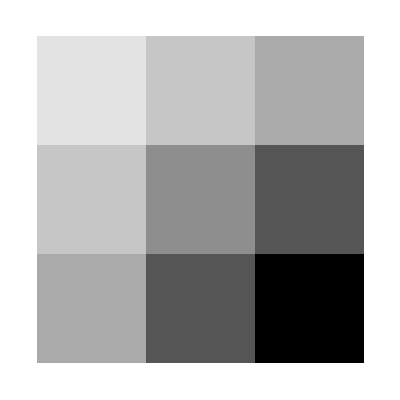

```mathematica
ArrayPlot[{{1,2,3},{2,4,6},{3,6,9}}]
```

```mathematica
Range/@Range[5]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

```mathematica
Trace[Range/@Range[5]]
```

{{Range[5],{1,2,3,4,5}},Range/@{1,2,3,4,5},{Range[1],Range[2],Range[3],Range[4],Range[5]},{Range[1],{1}},{Range[2],{1,2}},{Range[3],{1,2,3}},{Range[4],{1,2,3,4}},{Range[5],{1,2,3,4,5}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}}

```mathematica
ReplacePart[Range[10],a,{5,6,7}]
```

ReplacePart::partw: Part {5, 6, 7} of {1, 2, 3, 4, 5, 6, 7, 8, 9, 10} does not exist.

ReplacePart[{1,2,3,4,5,6,7,8,9,10},a,{5,6,7}]

```mathematica
Part[Range[10],{5,6,8}]
```

{5,6,8}

```mathematica
Part[Range[10],{{5},{6},{8}}]
```

Part::pkspec1: The expression {{5}, {6}, {8}} cannot be used as a part specification.

{1,2,3,4,5,6,7,8,9,10}⟦{{5},{6},{8}}⟧

```mathematica
plist={{4,4},{5,4},{6,4}}
```

{{4,4},{5,4},{6,4}}

```mathematica
Most[plist]
```

{{4,4},{5,4}}

```mathematica
Map[Most,plist]
```

{{4},{5},{6}}

```mathematica
??Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.

Attributes[Map]={Protected}
 
Options[Map]={Heads→False}